# SdS_4 Entropy Plots

7/20/2021
https://arxiv.org/pdf/gr-qc/0301090.pdf

#### As defined in the article, the radius equations for the dS black hole event horizon and the cosmological horizon,

r_b=(2M)/(3y)^(1/2)cos((π+ψ)/3)
r_c=(2M)/(3y)^(1/2)cos((π-ψ)/3)
where y=M^2/l^2 and l is related to Λ
and ψ=cos^-1(3(3y)^(1/2))

Note as y → 0 , r_bh → 2M  r_c → l  .

#### Then the surface gravity equations for the horizons of each,

k_b=α|M/r_bh^2-r_bh/l^2|
k_c=α|M/r_c^2-r_c/l^2|
where α=1/((1-(27y)^(1/3))^(1/2))

Note as y → 0 ,  k_bh → 1/(4M)  and  k_c → 1/l  .

#### Finally, the entropy eqn given in the paper for SdS,

S_SdS=π/k_bh^2+π/k_c^2+(2π)/(k_c k_bh)

Essentially, S_SdS is the summation of S_bh and S_c if S_bh=π/k_bh^2 and S_c=π/k_c^2 plus an extra term.

```mathematica
ClearAll["Global'*'"]
```

```mathematica
Subscript[k, b][M_,l_]:=(1/Sqrt[1-(27*M^2/l^2)^(1/3)])*Abs[M*((2*M)/Sqrt[3*(M^2/l^2)]*Cos[1/3*(Pi+ArcCos[3*Sqrt[3*M^2/l^2]])])^-2-1/l^2(2*M)/Sqrt[3*M^2/l^2]*Cos[1/3*(Pi+ArcCos[3*Sqrt[3*M^2/l^2]])]]
```

```mathematica
Subscript[k, c][M_,l_]:=(1/Sqrt[1-(27*M^2/l^2)^(1/3)])*Abs[M*((2*M)/Sqrt[3*(M^2/l^2)]*Cos[1/3*(Pi-ArcCos[3*Sqrt[3*M^2/l^2]])])^-2-1/l^2(2*M)/Sqrt[3*M^2/l^2]*Cos[1/3*(Pi-ArcCos[3*Sqrt[3*M^2/l^2]])]]
```

```mathematica
Subscript[S, SdS][M_,l_]:=Pi/(Subscript[k, b][M,l])^2+Pi/((Subscript[k, c][M,l])^2)+(2*Pi)/(Subscript[k, b][M,l]*Subscript[k, c][M,l])
```

#### Plot the Entropy vs mass (set l = 1),

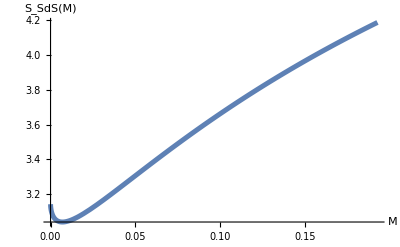

```mathematica
Plot[Subscript[S, SdS][M,1],{M,0,Sqrt[1/27]},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S_SdS(M)"},PlotStyle->{Thickness[0.009]}]
```

There’s a weird decrease in the entropy for small mass. I’m going to zoom in on the decrease just to see the values and what’s going on. In https://arxiv.org/pdf/gr-qc/0301090.pdf  the range for k_b and k_c are, (obtained by setting y -> 0  and y -> 1/27 in eqn (2).

(3Sqrt[3])/(4l)<k_b<Sqrt[3]/l →  l/Sqrt[3]<1/k_b<(4l)/(3Sqrt[3])
1/l<k_c<Sqrt[3]/l → l/Sqrt[3]<1/k_c<l

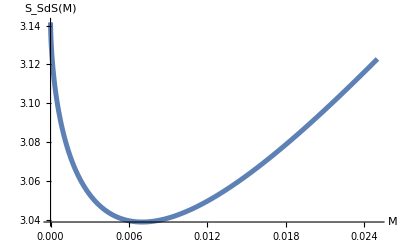

```mathematica
Plot[Subscript[S, SdS][M,1],{M,0,0.025},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S_SdS(M)"},PlotStyle->{Thickness[0.009]}]
```

#### Plot of the surface gravity of the black hole as a function of mass with l = 1,

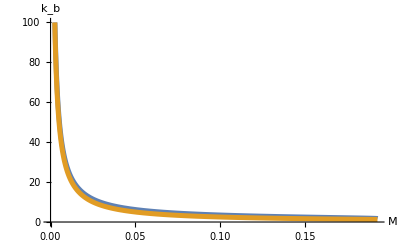

```mathematica
Plot[{Subscript[k, b][M,1],1/(4*M)},{M,0,Sqrt[1/27]},PlotRange->{0,100},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","k_b"},PlotStyle->{Thickness[0.009]}]
```

#### Plot of the surface gravity of the cosmological horizon as a function of mass with l = 1,

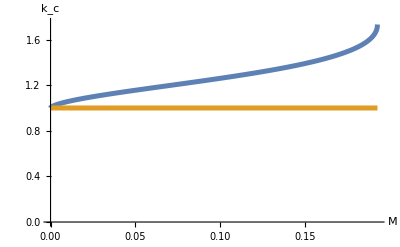

```mathematica
Plot[{Subscript[k, c][M,1],1},{M,0,Sqrt[1/27]},PlotRange->{0,1.75},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","k_c"},PlotStyle->{Thickness[0.009]}]
```

#### Plot the bh and cosmological entropies separately (S_b and S_c),

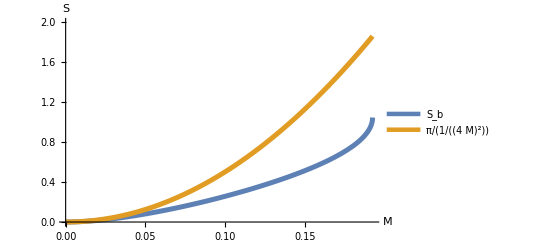

```mathematica
Plot[{Pi/(Subscript[k, b][M,1])^2,Pi/(1/(4*M))^2},{M,0,Sqrt[1/27]},PlotRange->{0,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S"},PlotStyle->{Thickness[0.009]},PlotLegends->{"S_b","π/(1/(4  M)^2)"}]
```

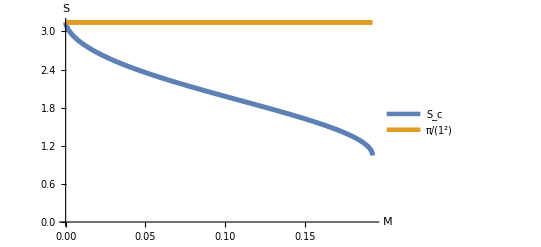

```mathematica
Plot[{Pi/(Subscript[k, c][M,1])^2,Pi/(1)^2},{M,0,Sqrt[1/27]},PlotRange->{0,Pi},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S"},PlotStyle->{Thickness[0.009]},PlotLegends->{"S_c","π/1^2"}]
```

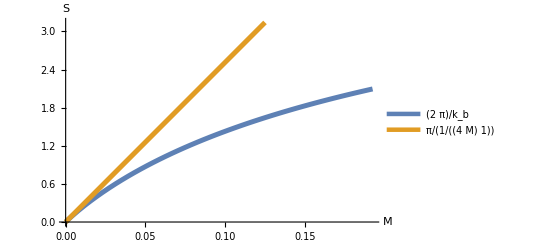

```mathematica
Plot[{(2*Pi)/((Subscript[k, b][M,1])*Subscript[k, c][M,1]),(2*Pi)/((1/(4*M))1)},{M,0,Sqrt[1/27]},PlotRange->{0,Pi},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S"},PlotStyle->{Thickness[0.009]},PlotLegends->{"(2  π)/k_b","π/(1/((4  M) 1))"}]
```

#### Plot S_b and S_c as functions of mass,

```mathematica
ClearAll["Global'*'"]
```

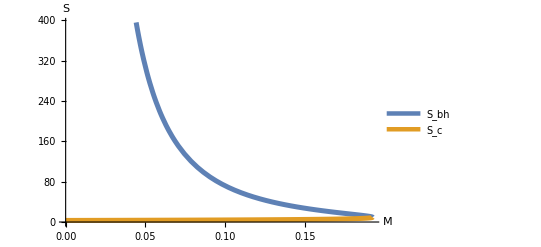

```mathematica
Plot[{Pi/((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi+ArcCos[3*Sqrt[3*M^2]])])^2,Pi/((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi-ArcCos[3*Sqrt[3*M^2]])])^2},{M,0,Sqrt[1/27]},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S"},PlotStyle->{Thickness[0.009]},PlotLegends->{"S_bh","S_c"}]
```

#### Now add the entropies vs M and see how it compares to nariai,

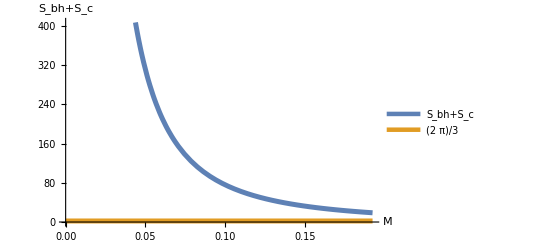

```mathematica
Plot[{Pi/((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi+ArcCos[3*Sqrt[3*M^2]])])^2+Pi/((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi-ArcCos[3*Sqrt[3*M^2]])])^2,(2*Pi)/3},{M,0,Sqrt[1/27]},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S_bh+S_c"},PlotStyle->{Thickness[0.009]},PlotLegends->{"S_bh+S_c","(2  π)/3"}]
```

#### Zoom in on the intersection point,

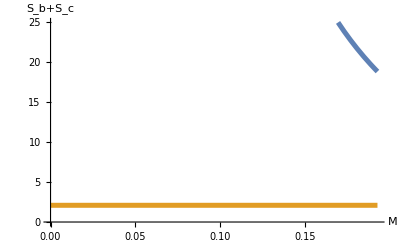

```mathematica
Plot[{Pi/((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi+ArcCos[3*Sqrt[3*M^2]])])^2+Pi/((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi-ArcCos[3*Sqrt[3*M^2]])])^2,(2*Pi)/3},{M,0,Sqrt[1/27]},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S_b+S_c"},PlotStyle->{Thickness[0.009]},PlotRange->{0,25}]
```

Hmm, S_b + S_c is wayyy higher than (2π)/3 . It approaches it when M > 1/Sqrtr[27] which I don’t think we want. We want it to approach it at that point because that’s where Nariai spacetime is, I think.

#### Let’s try using the generic entropy eqn, S = 1/4A instead of eqns 66 in the article, also found in https://arxiv.org/pdf/1408.5064.pdf in eqns (25) and (26),

This will give us S_b = π r_b^2 and S_c = π r_c^2  .

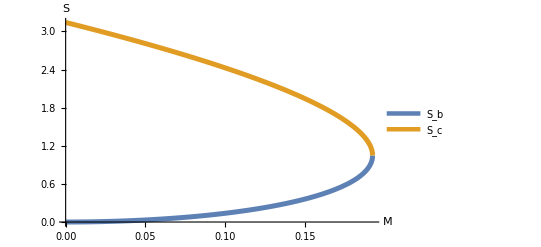

```mathematica
Plot[{Pi*((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi+ArcCos[3*Sqrt[3*M^2]])])^2,Pi*((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi-ArcCos[3*Sqrt[3*M^2]])])^2},{M,0,Sqrt[1/27]},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S"},PlotStyle->{Thickness[0.009]},PlotLegends->{"S_b","S_c"},PlotRange->{0,Pi}]
```

Note the point when the two entropies intersect. This is the Nariai spacetime!!

#### Now let’s add them,

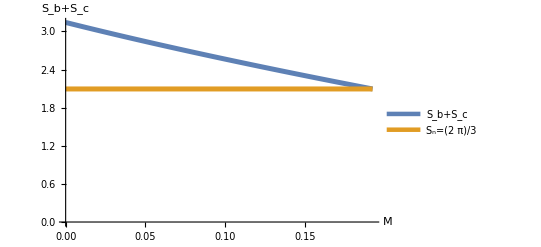

```mathematica
Plot[{Pi*((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi+ArcCos[3*Sqrt[3*M^2]])])^2+Pi*((2*M)/Sqrt[3*(M^2)]*Cos[1/3*(Pi-ArcCos[3*Sqrt[3*M^2]])])^2,(2*Pi)/3},{M,0,Sqrt[1/27]},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S_b+S_c"},PlotStyle->{Thickness[0.009]},PlotRange->{0,Pi},PlotLegends->{"S_b+S_c","S_n=(2  π)/3"}]
```

#### Simplifying r_b and r_c,

r_b=(2M)/((3(M/l)^2)^(1/2))cos(1/3(π+arccos[3Sqrt[3(M/l)^2]]))
    = (2M)/(M/l(3)^(1/2))cos(1/3(π+arccos[(3M)/l Sqrt[3]]))
    = (2l)/(3)^(1/2)cos(1/3(π+arccos[(3M)/l Sqrt[3]]))

r_c=(2M)/((3(M/l)^2)^(1/2))cos(1/3(π-arccos[3Sqrt[3(M/l)^2]]))
    = (2M)/(M/l(3)^(1/2))cos(1/3(π-arccos[(3M)/l Sqrt[3]]))
    = (2l)/(3)^(1/2)cos(1/3(π-arccos[(3M)/l Sqrt[3]]))

#### Series expansion of the entropies (the ones using S = 1/4A ) for small black hole, M << 1,

For cosmological entropy, S_c,

```mathematica
Simplify[Series[π((2 l)/(√3)Cos[1/3(π- ArcCos[3 M/l √3])])^2,{M,0,4}]]
```

l^2 π-2 (l π) M-2 π M^2-(5 π M^3)/l-(16 π M^4)/l^2+O[M]^5

For black hole entropy, S_b,

```mathematica
Simplify[Series[π((2 l)/(√(3(1/1)))Cos[1/3(π+ ArcCos[3 M/l √(3 1/1)])])^2,{M,0,4}]]
```

4 π M^2+(32 π M^4)/l^2+O[M]^5

“Black holes cause de Sitter cosmological entropy to decrease. The cosmological constant causes the black hole entropy to increase faster with mass.” - Dr. McGuigan in his notebook.

#### Compute the temperature of de Sitter and SdS black hole using,

β = T^-1=(∂S)/(∂M)

For black hole entropy, S_b,

```mathematica
D[(π((2M)/(√(3(M^2/1)))Cos[1/3(π+ ArcCos[3 √(3 M^2/1)])])^2), M]
```

(8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2))

For cosmological entropy, S_c,

```mathematica
D[(π((2M)/(√(3(M^2/1)))Cos[1/3(π- ArcCos[3 √(3 M^2/1)])])^2), M]
```

-(8 M π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2))

#### Plot the inverse temperatures as a function of mass,

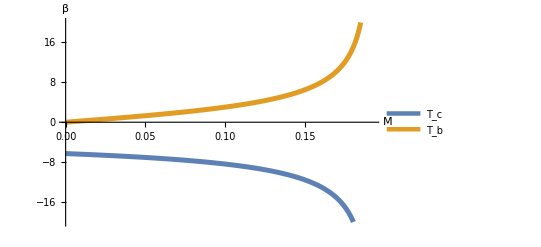

```mathematica
Plot[{-(8 M π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)),(8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2))},{M,0, √(1/27)},PlotRange->{-20,20}, BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","β"},PlotLegends->{"T_c","T_b"},PlotStyle->{Thickness[0.009]}]
```

So the cosmological temperature decreases as there’s more mass whereas the black hole’s temperature increases with more mass.

#### Plot the temperatures as a function of mass (invert the solutions from the partial derivative),

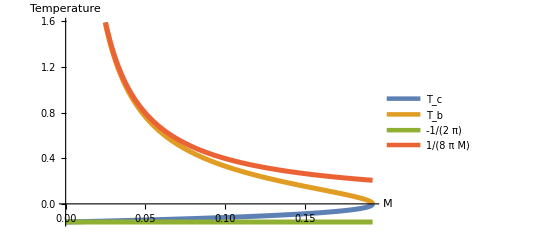

```mathematica
Plot[{-((8 M π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)))^-1,((8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)))^-1,-1/(2π), 1/(8π M)},{M,0, √(1/27)},PlotRange->{-(2π)^-1,(.2π)^-1}, PlotStyle->{Thickness[0.009]},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","Temperature"},PlotLegends->{"T_c","T_b", "-1/(2  π)","1/(8  π M)"}]
```

“This indicates Nariai spacetime is unstable with 0 temperature and de Sitter has T = -1/(2π) .” - Dr. McGuigan

#### Series expansions of the temperatures,

For the black hole inverse temperature, T_b^-1,

```mathematica
Series[(8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)),{M,0,8}]
```

8 π M+128 π M^3+2688 π M^5+61440 π M^7+O[M]^9

For the black hole temperature, T_b,

```mathematica
Series[((8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)))^-1,{M,0,8}]
```

1/(8 π M)-(2 M)/π+(√3 (-32/(√3)-16 √3) M^3)/(8 π)+(√3 (-448/(√3)-192 √3) M^5)/(8 π)-(2112 M^7)/π+O[M]^9

For the cosmological, dS temperature, T_c,

```mathematica
Series[-((8 π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3  √(1-27 M^2)))^-1,{M,0,8}]
```

-1/(2 π)+(√(M^2) M)/(M π)+(7 M^2)/(4 π)+(5 √(M^2) M^3)/(M π)+(273 M^4)/(16 π)+(64 √(M^2) M^5)/(M π)+(8151 M^6)/(32 π)+(1056 √(M^2) M^7)/(M π)+(1154725 M^8)/(256 π)+O[M]^9

“The black hole makes the de Sitter temperature decrease in absolute value. The cosmological constant makes the black hole temperature decrease.” - Dr. McGuigan

## Plugging in realistic values for M and seeing how the entropy changes.

Recall:  l = Sqrt[3/lambda]

#### First, avg stellar black hole in Planck masses M = 9.138*10^38,

```mathematica
Plot[Subscript[S, SdS][9.138*10^38,l],{l,0,10^60},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"M","S_SdS(M)"},PlotStyle->{Thickness[0.009]}]
```

-Graphics-

#### Zoom in,

```mathematica
Plot[Subscript[S, SdS][9.138*10^38,l],{l,0,10^40},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"l","S_SdS"},PlotStyle->{Thickness[0.009]},PlotLabel->"Entropy Avg Black Hole"]
```

-Graphics-

#### Change to kg because that looks kind of weird,

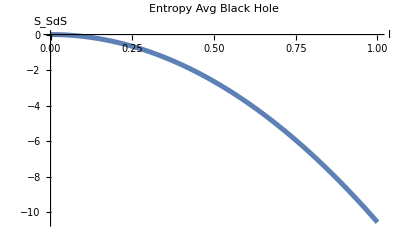

```mathematica
Plot[Subscript[S, SdS][1.989*10^31,l],{l,0,1},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"l","S_SdS"},PlotStyle->{Thickness[0.009]},PlotLabel->"Entropy Avg Black Hole"]
```

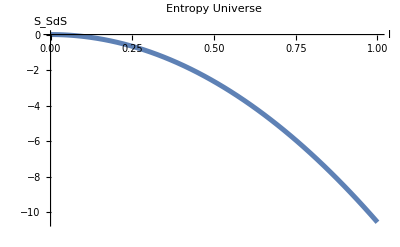

```mathematica
Plot[Subscript[S, SdS][10^53,l],{l,0,1},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"l","S_SdS"},PlotStyle->{Thickness[0.009]},PlotLabel->"Entropy Universe"]
```

```mathematica
Plot[Subscript[S, SdS][4.5940892*10^60,l],{l,0,1},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"l","S_SdS"},PlotStyle->{Thickness[0.009]},PlotLabel->"Entropy Universe"]
```

-Graphics-